## Introduction

The document investigates time ordering photon codes and their performance

## Assumptions and function definitions

```mathematica
nb=NotebookOpen["W:\\Projects\\Dbdoctor\\Dbdoctor.PhD\\Dbdoctor.PhD.Common\\Mathematica\\QFunc.nb"];
NotebookEvaluate[nb,InsertResults->False];
```

#### SeqA010672

Calculates the sequence A010672 in oeis.org

```mathematica
SeqA010672[n_]:=Module[{cands,A},
cands=Table[ii,{ii,1,n}];
A={};
While[Length[cands]>1,
AppendTo[A,Min[cands]];
];
Print[A];
]
```

```mathematica
PErr
```

```mathematica
SimpleSeq={1,2,3,4};(*average photon number =n/2*)
```

```mathematica
HH0H00V000 (*1,2,3,4     N=10, average photons per block = 4, Average number of photns per time bin n/N=0.4*)
```

```mathematica
(*Compare with PPM, all blocks are the same length*)
```

```mathematica
SeqA010672[n_]:=Module[{cands,A},
A={1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475,530,545,607,716,797,861,964,1059,1160,1306,1385,1434,1555,1721,1833,1933,2057,2260,2496,2698,2873,3060,3196,3331,3628,3711,3867,4139,4446,4639};
Print[A[[1;;n]]];
]
```

#### Perr

Calculates the probability for any combination of l loss errors and a add errors

```mathematica
Perr[l_,a_,n_,N_, pl_, pa_]:=Module[{},
Binomial[n,l]pl^l (1-pl)^(n-l)Binomial[N-n,a]pa^a(1-pa)^(N-n-a)
]
```

```mathematica
Perr[1,0,3,7,p1,p2]
```

3 (1-p1)^2 p1 (1-p2)^4

```mathematica
HH0V000 (*n=3, N=7*)
(**)
```

```mathematica
PSuccess=Perr[0,0,3,7,p,p]+Perr[1,0,3,7,p,p]+Perr[0,1,3,7,p,p];
PDetect=1-PSuccess
```

(1-p)^7+7 (1-p)^6 p

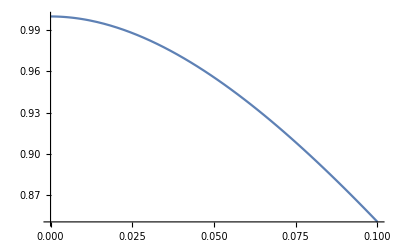

```mathematica
Plot[PSuccess, {p,0,0.1}]
```

```mathematica
SeqA010672[20]
```

{1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475}

```mathematica
ListPlot[SeqA010672[20]]
```

{1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475}

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null]

```mathematica
ListPlot[Null]
```

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null]

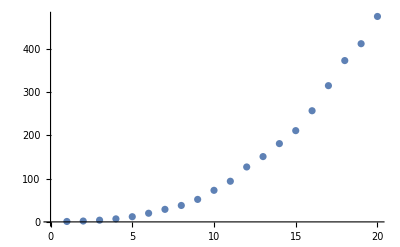

```mathematica
ListPlot[{1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475}]
```

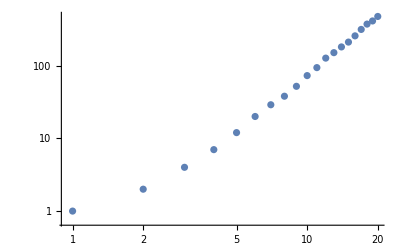

```mathematica
ListLogLogPlot[{1,2,4,7,12,20,29,38,52,73,94,127,151,181,211,257,315,373,412,475}]
```